This notebook covers bare-bones basic-differences between an uniform distribution and a normal distribution.  This is merely a preamble to setting up Monte - Carlo numerical integration for ordinary differential equations.

Author: Aneet Dharmavaram Narendranath, PhD (c) 2019

### Uniform vs Normal distribution

What is the distribution of data created by the Mathematica function, RandomReal[]?

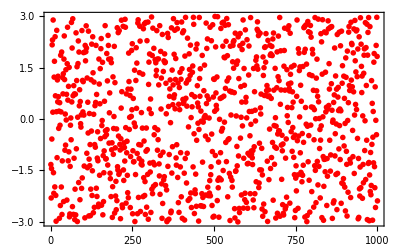

UniformDistribution[{-2.99903,2.9927}]

```mathematica
n=123;
SeedRandom[n];(*resets the pseudorandom generator,using n as a seed.*)
data1=RandomVariate[UniformDistribution[{-3,3}],1000];
lp1=ListPlot[data1,Frame->True,FrameStyle->Black,PlotStyle->{Red,PointSize[0.01]}]
FindDistribution[data1]
```

What does a Normal distribution look like?

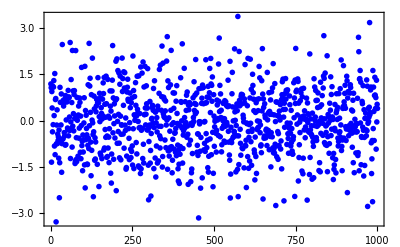

NormalDistribution[-0.0149788,1.01369]

```mathematica
n=123;
SeedRandom[n];
mu=0.;sig=0.5;
data2=RandomVariate[NormalDistribution[0,1],1000];
lp2=ListPlot[data2,Frame->True,FrameStyle->Black,PlotStyle->{Blue,PointSize[0.01]}]
FindDistribution[data2]
```

Compare a uniform distribution with a normal distribution

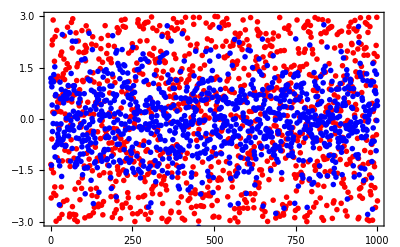

```mathematica
Show[lp1,lp2]
```

### Probability distributions

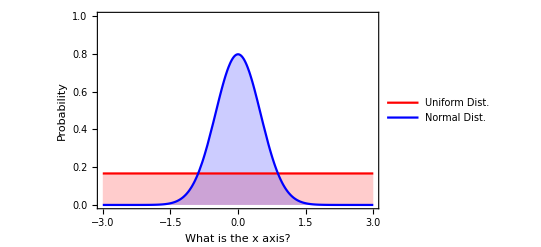

```mathematica
mu=0.;sig=0.5;
n=123;
SeedRandom[n];
Plot[
{PDF[UniformDistribution[{-3,3}],x],
PDF[NormalDistribution[mu,sig],x]},
{x,-3,3},Filling->Axis,Frame->True,FrameStyle->Black,PlotStyle->{Red,Blue},PlotRange->{All,{0,1}},FrameLabel->{"What is the x axis?", "Probability"},PlotLegends->{"Uniform Dist.","Normal Dist."}]
```

### Area under the probability distribution curve should be 1

```mathematica
{NIntegrate[PDF[UniformDistribution[{-3,3}],x],{x,-3,3}],NIntegrate[PDF[NormalDistribution[mu,sig],x],{x,-3,3}]}
```

{1.,1.}

### References

Lemons, D.S., "Introduction to stochastic processes in physics".